# Covid

## Analiza razlicnih aspektov epidemije v Sloveniji in po svetu

## Pridobivanje podatkov

Mathematica ima na voljo veliko podatkovno bazo Wolfram data repository.

```mathematica
ResourceSearch["COVID-19"]
```

ResourceObject::updav: There is an update available for resource "Epidemic Data for Novel Coronavirus COVID-19". Use ResourceUpdate[Epidemic Data for Novel Coronavirus COVID-19] to get the update.

ResourceObject::updav: There is an update available for resource "Genetic Sequences for the SARS-CoV-2 Coronavirus". Use ResourceUpdate[Genetic Sequences for the SARS-CoV-2 Coronavirus] to get the update.

General::stop: Further output of ResourceObject::updav will be suppressed during this calculation.

Posodobimo podatke:

```mathematica
ResourceUpdate["Epidemic Data for Novel Coronavirus COVID-19"];
```

Shranimo podatke:

```mathematica
podatki = ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];
```

```mathematica
podatki[[1;;10]](* prvih 10 vrstic podatkov *)
```

## Analiza primerov v Sloveniji

(Osnovni prikaz podatkov, par grafov)

```mathematica
Select[podatki, #["Country"] == LinguisticAssistant&]
```

```mathematica
potrjeniPrimeriSlovenija = %[[1]]["ConfirmedCases"]
```

TimeSeries[…]

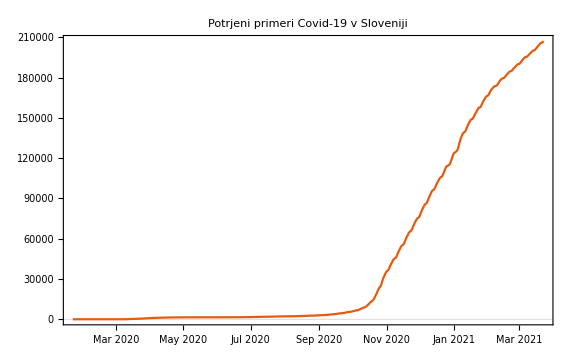

```mathematica
DateListPlot[potrjeniPrimeriSlovenija, PlotLabel->"Potrjeni primeri Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large]
```

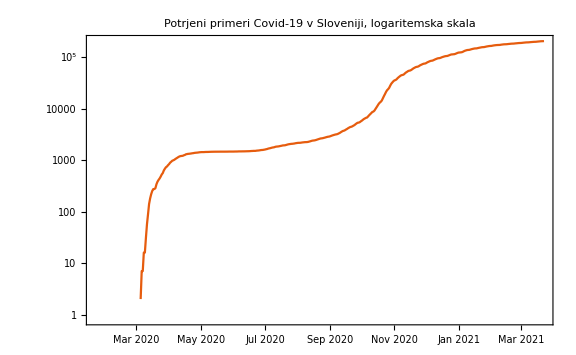

```mathematica
DateListLogPlot[potrjeniPrimeriSlovenija, PlotLabel->"Potrjeni primeri Covid-19 v Sloveniji, logaritemska skala", PlotTheme->"Scientific", ImageSize->Large]
```

Dnevno stevilo novih primerov:

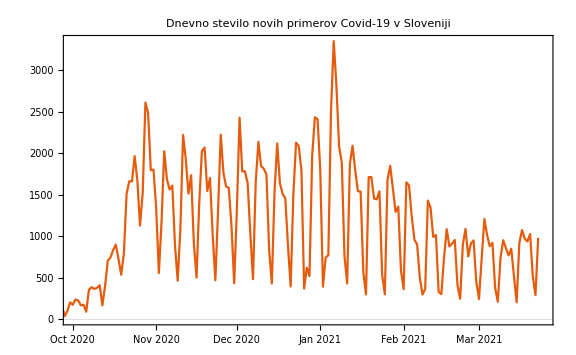

```mathematica
DateListPlot[Differences[potrjeniPrimeriSlovenija], PlotLabel->"Dnevno stevilo novih primerov Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large, PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic}]
```

Izracunamo 7-dnevno povprecje novih primerov v Sloveniji:

```mathematica
noviPrimeriSlovenija = MovingAverage[Differences[potrjeniPrimeriSlovenija], 7];
```

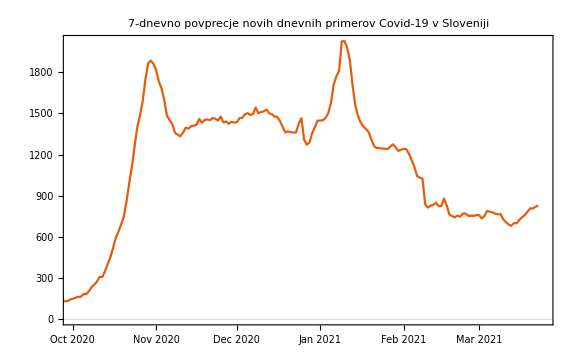

```mathematica
DateListPlot[noviPrimeriSlovenija, PlotLabel->"7-dnevno povprecje novih dnevnih primerov Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large,PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic} ]
```

Stevilo dnevnih novih primerov na 100.000 prebivalcev, 7-dnevno povprecje:

```mathematica
noviPrimeriNa100000Slovenija = 100000 * noviPrimeriSlovenija / LinguisticAssistant["Population"];
```

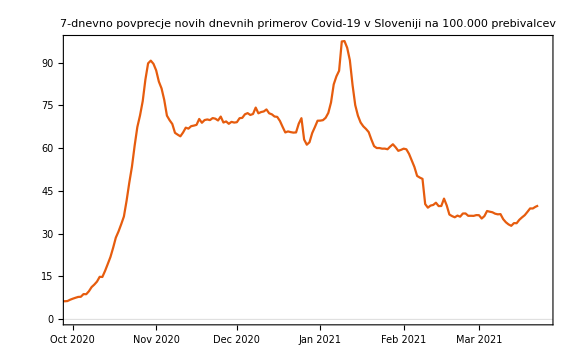

```mathematica
DateListPlot[noviPrimeriNa100000Slovenija, PlotLabel->"7-dnevno povprecje novih dnevnih primerov Covid-19 v Sloveniji na 100.000 prebivalcev", PlotTheme->"Scientific", ImageSize->Large,PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic} ]
```

## Novi primeri v odvisnosti od drzave

(Aplikacija v oblaku)

```mathematica
svetovniPodatki = ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"];
```

```mathematica
PrikaziNajnovejsePodatke[drzava_] := Module[{potrjeniPrimeri, potrjeniPrimeriNormalizirani, povprecje},
potrjeniPrimeri = Select[svetovniPodatki, #["Country"] == drzava&][[1]][["ConfirmedCases"]];
potrjeniPrimeriNormalizirani = 100000 * potrjeniPrimeri / drzava["Population"];
povprecje = MovingAverage[Differences[potrjeniPrimeriNormalizirani], 7];
DateListPlot[povprecje, PlotLabel->StringForm["7-dnevno povprecje novih dnevnih primerov Covid-19 za drzavo `` na 100.000 prebivalcev", ToUpperCase[drzava["Name"]]], PlotTheme->"Scientific", ImageSize->Large,PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic} ]
];
```

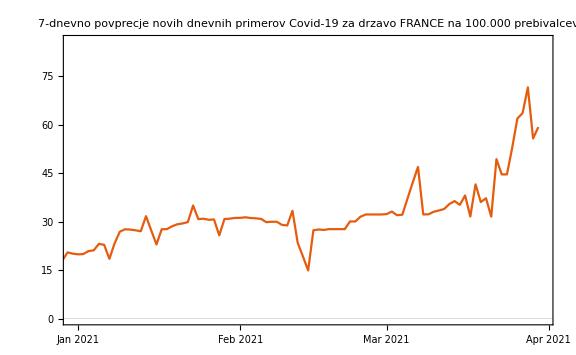

```mathematica
PrikaziNajnovejsePodatke[LinguisticAssistant]
```

```mathematica
obrazec = FormPage["drzava" -> "Country", PrikaziNajnovejsePodatke[#drzava] &,AppearanceRules-><|"Title" -> "Novi primeri okuzbe Covid-19", "Description" -> "Vnesi ime drzave, za katero zelis prikaz najnovejsih podatkov o novih primerih okuzbe s Covid-19.", "SubmitLabel" -> "Prikazi"|>]
```

```mathematica
CloudDeploy[obrazec, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/6972d519-fc3a-4515-95ed-5a202a83615e]

## Analiza smrtnosti v EU

(Naprednejsi prikaz podatkov, napovedovanje prihodnosti iz podatkov)

Poglejmo si, kako so podatki se dodatno razclenjeni:

```mathematica
ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]["ContentElements"]
```

{AustraliaProvinces,BrazilProvinces,CanadaProvinces,ChileProvinces,ChinaProvinces,ColombiaProvinces,Dataset,GermanyProvinces,IndiaProvinces,ItalyProvinces,JapanProvinces,MexicoProvinces,NetherlandsProvinces,PakistanProvinces,PeruProvinces,PuertoRicoProvinces,RawData,RussiaProvinces,SpainProvinces,SwedenProvinces,UkraineProvinces,USCounties,USStates,WorldCountries}

```mathematica
svetovniPodatki = ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"]
```

Dataset[<>]

Poglejmo si povprecno dnevno stevilo umrlih v zadnjem tednu na 100.000 prebivalcev v drzavah EU:

```mathematica
EUpodatki = Select[svetovniPodatki, MemberQ[EntityList[LinguisticAssistant], #["Country"]] &];
```

```mathematica
tabelaSmrti = #["Country"] -> 100000.0 * Mean[TimeSeriesWindow[#["Deaths"],{LinguisticAssistant, LinguisticAssistant}]]/#["Country"]["Population"]& /@ EUpodatki
```

```mathematica
GeoRegionValuePlot[tabelaSmrti, PlotLabel->"Smrti zaradi Covid-19 na 100.000 prebivalcev, povprecje zadnjih 7 dni"]
```

-Graphics-

Ali obstaja povezava med povprecno starostjo v drzavi in stevilom smrti za Covid-19?

```mathematica
tabelaStarostiInSmrti = {#["Country"]["MedianAge"],100000.0 * Mean[TimeSeriesWindow[#["Deaths"],{LinguisticAssistant, LinguisticAssistant}]]/#["Country"]["Population"]}-> #["Country"]["Name"]& /@ EUpodatki
```

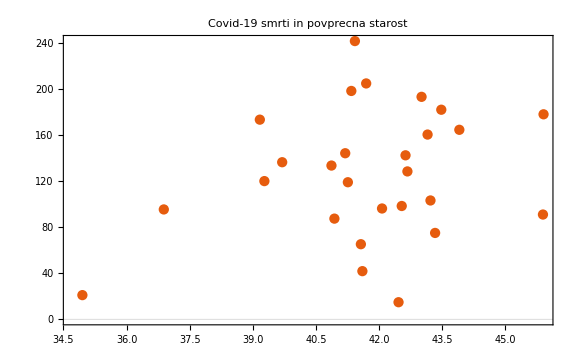

```mathematica
ListPlot[tabelaStarostiInSmrti, LabelingFunction->Tooltip, PlotLabel->"Covid-19 smrti in povprecna starost", PlotTheme->"Scientific", ImageSize->Large]
```

Ali je stevilo smrti povezano s povprecno starostjo? Poiscimo “najboljso” premico, ki se prilega danim podatkom. To je premica, za katero velja, da je vsota vseh razdalj podatkovnih tock do nase premice kar najmanjsa mozna. Ta premica se imenuje regresijska premica. Pricakujemo, da bo ta premica imela pozitivni smerni koeficient.

```mathematica
podatkiOStarostiInSmrti = QuantityMagnitude[Normal[{#["Country"]["MedianAge"],100000.0 * Mean[TimeSeriesWindow[#["Deaths"],{LinguisticAssistant, LinguisticAssistant}]]/#["Country"]["Population"]}& /@ EUpodatki]]
```

{{41.195,144.231},{45.908,178.049},{43.152,160.457},{45.894,90.9792},{39.697,136.423},{41.425,241.675},{42.07,96.2316},{41.258,119.039},{41.34,198.339},{43.907,164.586},{40.868,133.532},{41.693,204.865},{43.221,103.196},{39.166,173.398},{43.478,182.03},{42.628,142.427},{43.331,74.988},{36.884,95.4054},{41.603,41.7975},{42.673,128.435},{43.009,193.226},{41.567,65.2008},{42.538,98.3966},{42.462,14.8043},{39.274,120.02},{34.949,20.9694},{40.938,87.4251}}

Poiscemo najboljso premico:

```mathematica
najboljsaPremica = LinearModelFit[podatkiOStarostiInSmrti, x, x]
```

FittedModel[-131.609+6.18364 x]

Prikazemo podatke in regresijsko premico:

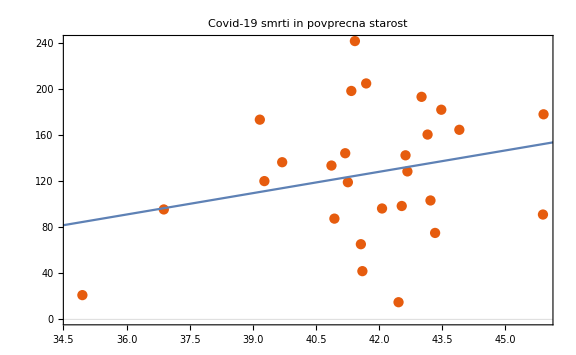

```mathematica
Show[ListPlot[tabelaStarostiInSmrti, LabelingFunction->Tooltip, PlotLabel->"Covid-19 smrti in povprecna starost", PlotTheme->"Scientific", ImageSize->Large],
Plot[najboljsaPremica["BestFit"], {x, 0, 50}]]
```

Regresijska premica nam podaja “povprecno odvisnost” glede na dane podatke. Z njeno pomocjo lahko razumemo bolje podatke ali napovemo neznano. Slovenija je na grafu visje od premice (njena smrtnost je glede na stevilo prebivalcev visja od premice, ki predstavlja povprecje). Najbolje gre Finski.

## Zdravniski podatki o pacientih

(Podrobnejsa specificna analiza podatkov)

### Pridobivanje podatkov

Najprej uvozimo podatke o pacientih.

```mathematica
podatki = ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"]
```

Global`DateInterval::shdw: Symbol DateInterval appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Dataset[<>]

Iz katerih drzavi imamo podatke?

```mathematica
ReverseSortBy[Tally[#["Country"]&/@ podatki], Last]
```

Prikazemo na zemljevidu:

```mathematica
GeoHistogram[podatki[All,"GeoPosition"], ImageSize->Large, PlotTheme->"Scientific", PlotLegends->Automatic]
```

-Graphics-

Porazdelitev starosti pacientov:

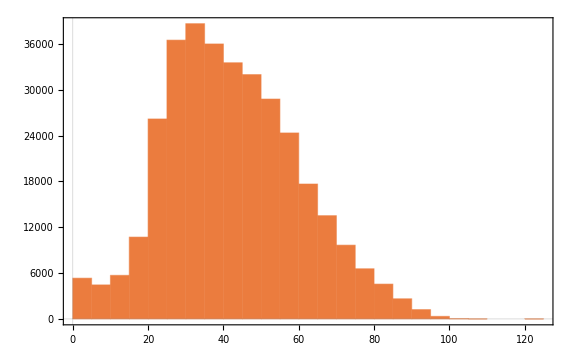

```mathematica
Histogram[Select[podatki[All, "Age"], NumberQ[#]&], PlotTheme->"Scientific", ImageSize->Large]
```

### Kronicne bolezni

```mathematica
podatki[Select[#["ChronicDiseaseQ"] == True&],"ChronicDiseases"]
```

Zelo malo okuzenih (v nasih podatkih) ima pridruzene kronicne bolezni. Najbolj pogoste so:

```mathematica
Take[ReverseSortBy[Tally[DeleteMissing[Flatten[%]]], Last], 10]
```

### Simptomi

```mathematica
Take[ReverseSortBy[Tally[DeleteMissing[Flatten[podatki[All, "Symptoms"]]]], Last], 20]
```

### Umrli

Katere simptome so imeli tisti pacienti, ki so na koncu umrli?

```mathematica
Take[ReverseSortBy[Tally[DeleteMissing[Flatten[podatki[Select[#["DeathQ"] == True&], "Symptoms"]]]], Last], 20]
```